# ASEN 5007-Homework 4

## Zach Dischner & Pierce Martin

## Setup and pre-reqs

### Helpful modules

Cell 7: Simple function to print output for solutions in a stylazed way

```mathematica
PrintWithStyle[x_] := Module[{color=LightGreen},Framed[Style[x,18,Bold,Background->color],
Background->color]
]
```

```mathematica
Provided Code
```

```mathematica
My Code
```

3 x^2-Cos[x]

3 x^2-Cos[x]

## Problem 8.2

Code from problem 8.1, used as reference

```mathematica
(*Exercise 8.1-Master-Slave Method*)(*MFC:u2-u6=1/5-slave:u6*)MasterStiffnessOfSixElementBar[kbar_]:=Module[{K=Table[0,{7},{7}]},K[[1,1]]=K[[7,7]]=kbar;For[i=2,i≤6,i++,K[[i,i]]=2*kbar];
For[i=1,i≤6,i++,K[[i,i+1]]=K[[i+1,i]]=-kbar];Return[K]];
FixLeftEndOfSixElementBar[Khat_,fhat_]:=Module[{Kmod=Khat,fmod=fhat},fmod[[1]]=0;Kmod[[1,1]]=1;Kmod[[1,2]]=Kmod[[2,1]]=0;Return[{Kmod,fmod}]];
K=MasterStiffnessOfSixElementBar[100];(*Print["Stiffness K=",K//MatrixForm];*)f={1,2,3,4,5,6,7};(*Print["Applied forces=",f];*)T={{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,1,0,0,0,0},{0,0,0,0,0,1}};
(*Print["Transformation matrix T=",T//MatrixForm];*)
g={0,0,0,0,0,-1/5,0};
(*Print["Constraint gap vector g=",g];*)
Khat=Simplify[Transpose[T].K.T];fhat=Simplify[Transpose[T].(f-K.g)];
{Kmod,fmod}=FixLeftEndOfSixElementBar[Khat,fhat];(*fix left end*)(*Print["Modified Stiffness upon fixing node 1:",Kmod//MatrixForm];*)
(*Print["Modified RHS upon fixing node 1:",fmod];*)
umod=LinearSolve[Kmod,fmod];
(*Print["Computed umod (lacks slave u6)=",umod];*)
u=T.umod+g;(*Print["Complete solution u=",u];*)
(*Print["Numerical u=",N[u]];*)
fu=K.u;(*Print["Recovered forces K.u with reactions=",fu];
Print["Numerical K.u=",N[fu]];*)
```

Supplied code to automate the formation of T and g. Solved here and by hand as a verification check. The slaves (u4,u5,u6) were all solved for in terms of their masters, so as to then remove those variables from the equations.

```mathematica
sol=Simplify[Solve[{u2-u6==1/5,u3+2*u4==-2/3,2*u3-u4+u5==0},{u4,u5,u6}]];ums={u1,u2,u3,u4,u5,u6,u7}/.sol[[1]];
um={u1,u2,u3,u7};T=Table[Coefficient[ums[[i]],um[[j]]],{i,1,7},{j,1,4}];g=ums/.{u1->0,u2->0,u3->0,u4->0,u5->0,u6->0,u7->0};
Print["Transformation matrix T=",T//MatrixForm];
Print["Gap vector g=",g];
```

Transformation matrix T=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | -1/2 | 0
0 | 0 | -5/2 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

Gap vector g={0,0,0,-1/3,-1/3,-1/5,0}

## Problem 9.1 Re-treat problem 8.1, now using the penalty functoin method with a MFC being (u2-u6=1/5). Using book supplied code:

```mathematica
SquareRootRule[k_,p_] := Module[{A},A=10^(k+p/2);Return[A]];
```

Stiffness K=(100 | -100 | 0 | 0 | 0 | 0 | 0
-100 | 200 | -100 | 0 | 0 | 0 | 0
0 | -100 | 200 | -100 | 0 | 0 | 0
0 | 0 | -100 | 200 | -100 | 0 | 0
0 | 0 | 0 | -100 | 200 | -100 | 0
0 | 0 | 0 | 0 | -100 | 200 | -100
0 | 0 | 0 | 0 | 0 | -100 | 100)

Applied forces={1,2,3,4,5,6,7}

Weight w=1.×10^3 u={0., 0.2700000000000002, 0.2809756097560978, 0.2619512195121954, 0.20292682926829292, 0.09390243902439045, 0.16390243902439044}

Weight w=1.×10^4 u={0., 0.27, 0.2756109725685786, 0.2512219451371571, 0.1868329177057357, 0.07244389027431426, 0.14244389027431426}

Weight w=1.×10^5 u={0., 0.2700000000000038, 0.2750612346913309, 0.25012246938265814, 0.18518370407398524, 0.07024493876531243, 0.14024493876531244}

Weight w=1.×10^6 u={0., 0.2699999999998538, 0.27500612484673254, 0.2500122496936114, 0.18501837454049025, 0.07002449938736907, 0.14002449938736908}

Weight w=1.×10^7 u={0., 0.27000000000071184, 0.27500061249918056, 0.2500012249976493, 0.18500183749611812, 0.07000244999458685, 0.14000244999458686}

Weight w=1.×10^8 u={0., 0.2699999999928628, 0.2750000612428475, 0.25000012249283216, 0.18500018374281682, 0.07000024499280151, 0.1400002449928015}

Weight w=1.×10^9 u={0., 0.2699999999505213, 0.27500000607552116, 0.250000012200521, 0.18500001832552085, 0.07000002445052068, 0.14000002445052068}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1., 0., 0., 0., 0., 0., 0.}, {0., 1.×10^10, -100., 0., 0., -1.×10^10, 0.}, {0., -100., 200., -100., 0., 0., 0.}, « 1 », {0., 0., 0., -100., 200., -100., 0.}, {0., -1.×10^10, 0., 0., -100., 1.×10^10, -100.}, {0., 0., 0., 0., 0., -100., 100.}} may contain significant numerical errors.

Weight w=1.×10^10 u={0., 0.2700000018070315, 0.2750000024195315, 0.2500000030320315, 0.1850000036445315, 0.07000000425703148, 0.1400000042570315}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1., 0., 0., 0., 0., 0., 0.}, {0., 1.×10^11, -100., 0., 0., -1.×10^11, 0.}, {0., -100., 200., -100., 0., 0., 0.}, « 1 », {0., 0., 0., -100., 200., -100., 0.}, {0., -1.×10^11, 0., 0., -100., 1.×10^11, -100.}, {0., 0., 0., 0., 0., -100., 100.}} may contain significant numerical errors.

Weight w=1.×10^11 u={0., 0.2699999989599998, 0.2749999990212498, 0.2499999990824997, 0.18499999914374976, 0.06999999920499982, 0.1399999992049998}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1., 0., 0., 0., 0., 0., 0.}, {0., 1.×10^12, -100., 0., 0., -1.×10^12, 0.}, {0., -100., 200., -100., 0., 0., 0.}, {0., 0., « 3 », 0., 0.}, {0., 0., 0., -100., 200., -100., 0.}, {0., -1.×10^12, 0., 0., -100., 1.×10^12, -100.}, {0., 0., 0., 0., 0., -100., 100.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve :: luc will be suppressed during this calculation.

Weight w=1.×10^12 u={0., 0.26999999989600004, 0.27499999990212504, 0.24999999990825003, 0.18499999991437505, 0.06999999992050006, 0.13999999992050008}

Weight w=1.×10^13 u={0., 0.26999999998959995, 0.2749999999902124, 0.24999999999082495, 0.18499999999143746, 0.06999999999204995, 0.13999999999204996}

Weight w=1.×10^14 u={0., 0.26999999999896, 0.2749999999990213, 0.24999999999908254, 0.18499999999914377, 0.06999999999920505, 0.13999999999920504}

Weight w=1.×10^15 u={0., 0.26999999999989593, 0.27499999999990205, 0.24999999999990816, 0.18499999999991426, 0.06999999999992043, 0.13999999999992044}

Weight w=1.×10^16 u={0., 0.26999999999998964, 0.2749999999999903, 0.24999999999999095, 0.18499999999999153, 0.0699999999999921, 0.1399999999999921}

Weight w=1.×10^17 u={0., 0.3309523809523796, 0.3359523809523797, 0.31095238095237976, 0.24595238095237984, 0.13095238095237993, 0.2009523809523799}

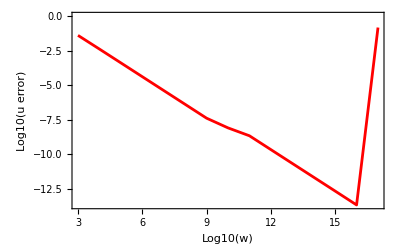

```mathematica
(*Exercise 9.1-Penalty Method*)(*MFC:u2-u6=1/5 variable w*)K=MasterStiffnessOfSixElementBar[100];
Print["Stiffness K=",K//MatrixForm];
f={1,2,3,4,5,6,7};Print["Applied forces=",f];uexact={0,0.27,0.275,0.25,0.185,0.07,0.14};ew={};
For[w=100,w≤10^16,w=10*w;(*increase w by 10 every pass*)Khat=K;fhat=f;
Khat[[2,2]]+=w;Khat[[6,6]]+=w;Khat[[6,2]]=Khat[[2,6]]-=w;
fhat[[2]]+=(1/5)*w;fhat[[6]]-=(1/5)*w;(*insert penalty*){Kmod,fmod}=FixLeftEndOfSixElementBar[Khat,fhat];
u=LinearSolve[N[Kmod],N[fmod]];
Print["Weight w=",N[w]//ScientificForm," u=",u//InputForm];
e=Sqrt[(u-uexact).(u-uexact)];
(*Print["L2 solution error=",e//ScientificForm];*)AppendTo[ew,{Log[10,w],Log[10,e]}];];
ListLinePlot[ew,AxesOrigin->{5,-8},Frame->True,PlotStyle->{AbsolutePointSize[4],AbsoluteThickness[2],RGBColor[1,0,0]},AxesLabel->{"Log10(w)","Log10(u error)"}]
```

```mathematica
k=Floor[Log[10,Max[K]]];
p =16;
w_srr=Log[10,SquareRootRule[k,p]]
```

10

```mathematica
PrintWithStyle["The minimum error occurs for a weighting of w=16"]
PrintWithStyle["Square Root Rule predicts that [ w = 10 ]. Agreement is poor"]
```

The minimum error occurs for a weighting of w=16

Square Root Rule predicts that [ w = 10 ]. Agreement is poor

## Problem 9.5

Part A)
	Solved for T and g by hand, then solved for uhat

```mathematica
ClearAll["Global`*"]
```

```mathematica
T = {{1, 0}, {1, 0}, {0, 1}};Print["Transformation Matrix: ",T //MatrixForm]
f={P,0,0};Print["Force ",f//MatrixForm];
g = {0, 0, 0}; Print["Constraint Gap Vector: ",g //MatrixForm]
K = {{EE*A/L, 0, 0}, {0, 12*EE*II/L^3, 6*EE*II/L^2}, {0, 6*EE*II/L^2, 4*EE*II/L}}; Print[K // MatrixForm]
P = α*EE*A;
II= β*A*L^2;
K = {{EE*A/L, 0, 0}, {0, 12*EE*II/L^3, 6*EE*II/L^2}, {0, 6*EE*II/L^2, 4*EE*II/L}}; 
Print["K with substitutions:", K // MatrixForm]
Khat=Simplify[Transpose[T].K.T];fhat=Simplify[Transpose[T].(f-K.g)];
Print["Khat:",Khat//MatrixForm];Print["fhat:",fhat//MatrixForm]
uhat = LinearSolve[Khat,fhat];
Print["Solved for u = ",uhat//MatrixForm]
```

Transformation Matrix: (1 | 0
1 | 0
0 | 1)

Force (A EE α
0
0)

Constraint Gap Vector: (0
0
0)

((A EE)/L | 0 | 0
0 | (12 A EE β)/L | 6 A EE β
0 | 6 A EE β | 4 A EE L β)

K with substitutions:((A EE)/L | 0 | 0
0 | (12 A EE β)/L | 6 A EE β
0 | 6 A EE β | 4 A EE L β)

Khat:((A EE (1+12 β))/L | 6 A EE β
6 A EE β | 4 A EE L β)

fhat:(A EE α
0)

Solved for u = ((L α)/(1+3 β)
-(3 α)/(2 (1+3 β)))

Part b)
	Penalty method. First construct the penalty stiffness matrix.

```mathematica
(*Form the penalty weighting matrix, then add to original K*)
wmat = w*{{1, -1,0}, {-1, 1, 0}, {0, 0, 0}};
(*Amat = {{1,-1,0}};
Bmat = {{0}};
Wmat = {{w}};
Khat = K+Transpose[Amat].Wmat.Amat;
fhat = f+Wmat.Transpose[Amat].Bmat;*)
Khat = K + wmat; Print["Modified Khat (penalty method): ", Khat // MatrixForm]
u = FullSimplify[LinearSolve[Khat,f]];
Print["u: ", u//MatrixForm]
uLimit=Limit[u,w->Infinity];
Print["Limit as w->Infinity: ",uLimit//MatrixForm]
PrintWithStyle["Limit as w->Infinity: "]PrintWithStyle[uLimit]
PrintWithStyle["These match what I obtained from 9.5 a), using the master-slave method. Cool!"]
PrintWithStyle["The penalty stiffness can be physically interpreted by adding another member that interacts with 
				existing ones. The interaction 'w' is likened to EA/L, 
				which defines the 'stiffness' of that interaction. 
				High w would mean a completely rigid link where applied"]
```

Modified Khat (penalty method): ((A EE)/L+w | -w | 0
-w | w+(12 A EE β)/L | 6 A EE β
0 | 6 A EE β | 4 A EE L β)

u: ((L α (L w+3 A EE β))/(3 A EE β+L (w+3 w β))
(L^2 w α)/(L w+3 A EE β+3 L w β)
-(3 L w α)/(2 L w+6 A EE β+6 L w β))

Limit as w->Infinity: ((L α)/(1+3 β)
(L α)/(1+3 β)
-(3 α)/(2+6 β))

Limit as w->Infinity:  {(L α)/(1+3 β),(L α)/(1+3 β),-(3 α)/(2+6 β)}

These match what I obtained from 9.5 a), using the master-slave method. Cool!

The penalty stiffness can be physically interpreted by adding another member that interacts with existing ones. The interaction 'w' is likened to EA/L, which defines the 'stiffness' of that interaction. High w would mean a completely rigid link where applied

Part c)
	Re-solve using Lagrangian multipliers

```mathematica
AugMat = {{1,-1,0}};
K = {{EE*A/L, 0, 0}, {0, 12*EE*II/L^3, 6*EE*II/L^2}, {0, 6*EE*II/L^2, 4*EE*II/L}};
Khat = {K,AugMat};
K2 = Append[K,AugMat[[1]]];
AugMat2 = Append[AugMat[[1]],0];
Khat=Append[Transpose[K2],AugMat2];
Print["Khat: ",Khat//MatrixForm]
uhat = Append[u,λ];
fhat = Append[f,0];
u = FullSimplify[LinearSolve[Khat,fhat]];
PrintWithStyle["u: "]PrintWithStyle[ u//MatrixForm]
PrintWithStyle["Same solutino as a). Yay!"]
```

Khat: ((A EE)/L | 0 | 0 | 1
0 | (12 A EE β)/L | 6 A EE β | -1
0 | 6 A EE β | 4 A EE L β | 0
1 | -1 | 0 | 0)

u:  ((L α)/(1+3 β)
(L α)/(1+3 β)
-(3 α)/(2+6 β)
(3 A EE α β)/(1+3 β))

Same solutino as a). Yay!